# Video Traking

User interface for video traking by Karolis Misiunas. 
Warning: The routine works slightly differently on Mac and Windowns since M9+ because FFmpeg library is not compatable.

ToDo:
 - [ ] Add multiple ROI processing in UI
 - [ ] Reporting: Running analysis reporting as Monitor[]
 - [ ] FFmpeg: optimise for speed (it is not a bottle neck, but would be nice to have additional ~15%
 - [ ] Processing: run on multiple cores - will speed it up a lot!
 - [ ] Localised intensity correction for treshhold
 - [ ] FFImport frame count is not working properly or relies on Import[]
 - find out what happens when there is poor particle and a good one in intire analysis - might be we include them as singles?!

```mathematica
Quit[];
```

```mathematica
<<VideoAnalysis`
$HistoryLength = 2; (*prevent memory overload*)
SetOptions[FFmpeg, 
  "Colors"->1 (*number of color channels*),
  "ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
];
SetOptions[VideoIO,
  "FrameIdFromFrame"-> True,
  "Import" -> FFImport
];
```

## Under the hood functions

```mathematica
FindIntervals[raw_]:= Module[{list},
  list = Sort[ DeleteDuplicates[raw]];
  If[ Length[list] == 0, Return[{}]]; 
  Append[ 
  Reap[FoldList[
    If[#2-Last[#1]==1,
      Append[#1,#2],
      If[Length[#1]==1, Sow[First[#1]], Sow[Interval[{First[#1],Last[#1]}]]];
      {#2}] & ,
    {First[raw]},
    Rest[list]]][[-1,1]],Last[list] 
  ] 
];

processVideo[file_] := Module[{loadTime, analysisTime,oldROI,outputFolder, problems},
  Clear[output];
  oldROI = ROICurrent[] ; (*reuse ROI*)
  Print@Style["===================== " ~~ FileNameTake[file] ~~" =====================", Orange];

  (* === Analyse === *)
  VideoSelect[ file ];
  ROISelect[ oldROI ];
  loadTime = First@AbsoluteTiming[ VideoBufferAll[] ];
  BackgroundUpdate[];
  (*BackgroundUpdate@bgAssociation[ VideoFile[]];*)
  {analysisTime,output} = AbsoluteTiming @ VideoAnalyse[];

  (* === Report === *)
  problems = VideoProblemInFrames[]⟦;;,1⟧;
  Print[ "Analysis took (load + recognition): "<> ToString@loadTime <> " + "<> ToString@analysisTime<>" = "<> ToString@(loadTime+analysisTime)<>" sec"];
  Print["Particles found: " ,Style[Length[output], Green], ", and problems were in ", Style[Length[problems], Red] , " frames"];
  (*show detection frequancy*)
  (*Print @ NumberLinePlot[
    { (*FindIntervals[output⟦All, 1⟧],*) FindIntervals[problems]},
    ImageSize->Full
  ];*)
  (* show background and a selection of bad frames *)
  Print @ Grid[ Partition[
    {Column[{"Background", BackgroundCurrent[]}]}   ~Join~
   If[Length[problems]>1,(Column[{Style[#, Red], VideoGet[#]}] &/@ Sort@RandomChoice[problems,14] ), {}]
  , 5]];
  

  (* === Post Process === *)

  (* mark frames with problems as LQPos *)
  (output⟦#,5⟧ = 0)&/@Position[output⟦;;,1⟧ , _Integer?(MemberQ [problems, #]&)]; 
  (*update time and positions to absolute ones*)
  cornerPos = ROICurrent[]⟦1⟧;
  output⟦All,1⟧ = VideoFrameID /@ output⟦All,1⟧ ; (*time*)
  output⟦All,2⟧ = output⟦All,2⟧ + cornerPos⟦1⟧ ; (*x*)
  output⟦All,3⟧ = output⟦All,3⟧ + cornerPos⟦2⟧ ; (*y*)
  (* save to file *)
  outputFolder = FileNameJoin[{DirectoryName[file],"raw_points"}];
  If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

  Print["Done: "<>
  ToString@Export[ FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  output]];
]
```

#### Backgroud pre-computation

```mathematica
(* Input: must be structured file names *)
(* Returns: "bgAssociation" association: file -> background img *)
(* Warning this is less efficiant than default method*)
prepareBackgroundImages[filesAll_, clusterSize_] := Module[
  {clusters, processCluster, roi,  getAllImages},
  roi = ROICurrent[];
  clusters = Partition[filesAll, clusterSize, clusterSize,{1,1},{}];
  (*special case*)
  If[Length @ Last @ clusters < clusterSize,  (* attach to the last cluster*)
    clusters = Append[clusters⟦;;-3⟧, Join[clusters⟦-1⟧,clusters⟦-2⟧]];
  ];

  processCluster[files_]:= Module[
	{allImages, selectedImages},
	allImages = Select[ImageQ] @ Flatten[getAllImages/@files];
	selectedImages = RandomSample[allImages, 20000];
	Image[Median[ImageData/@ selectedImages ]] (*median algorithm*)
  ];

  (* obtain all images *) 
  getAllImages[file_] := Module[{},
	VideoSelect[file];
	ROISelect[roi];
    VideoBufferAll[];
	VideoGet /@ Range[VideoLength[]]
  ];

  Print["Pre-computing background images for ", Length[filesAll], " files"];
  Monitor[
	bgImages = Table[
		(Print["Cluter ", i, " → ", #]; #) &@  processCluster[clusters⟦i⟧] ,
		{i, 1, Length[clusters]}
	],
	Row[{"Analysing clusters: ",ProgressIndicator[i,{1,Length[clusters]}],i}," "]
  ];
  
  bgAssociation = Join @@ Table[
		AssociationMap[ bgImages⟦i⟧ &, clusters⟦i⟧ ] ,
		{i, 1, Length[clusters]}
	];
  Print["Finised analysing all the backround images"];
];
```

## Step 1 - Select sample video file

```mathematica
VideoSelect["E:\\2016-06-20\\2\\200fps_s1.avi"]
```

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

VideoAddProcessRawFrame: new function count is 1

200fps_s1.avi has 9998 frames and is 96x700

## Step 2 - Select region of intrest

```mathematica
ROISelect[]
```

{{34,410},{70,426}}

```mathematica
ROISelect[{{34,410},{70,426}} ]
```

{{34,410},{70,426}}

## Step 3 - Configure tracing algorithm

```mathematica
Options[VideoTracking];

(* Light Particles *)
SetOptions[VideoTracking, 
"FilterElongation" -> {0.0, 0.6},
 "FilterArea" -> {8,33},
 "UpdateBackgroung" -> False,
 Threshold -> 0.07,
"ForegroundMethod"->"Bright" 
];
```

```mathematica
(* Dark Particles *)
SetOptions[VideoTracking, 
 "FilterElongation" -> {0.0, 0.4},
 "FilterArea" -> {12,38},
 "UpdateBackgroung" -> False,
 Threshold -> 0.14,
"ForegroundMethod"->"Dark" 
];
```

## Step 4 - Test configuration

```mathematica
VideoBufferAll[]
```

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

```mathematica
VideoGet[20000]
```

-Graphics-

```mathematica
VideoFindThreshold[]
```

```mathematica
BackgroundUpdate[]
```

-Graphics-

```mathematica
findFrameNo[frameId_]:= Which[
VideoFrameID[1] ≤  frameId ≤ VideoFrameID[VideoLength[]], 
	frameId - VideoFrameID[1]+1,
frameId > VideoFrameID[VideoLength[]],
	Print["Go forward by ",N[(frameId - VideoFrameID[1])/VideoLength[]], " vidoes"],
VideoFrameID[1] >  frameId ,
	Print["Go back by ",N[-(frameId - VideoFrameID[1])/VideoLength[]+1], " vidoes"]
];
```

#### Analyse Single Frame

{{410,65.274,675.006,0.,1.,1.427,1.673,0.266},{410,4.79,655.035,0.,1.,1.171,1.922,0.451},{410,45.327,637.925,0.,1.,1.696,1.658,0.158},{410,45.157,627.392,0.,1.,1.687,1.727,0.187},{410,85.569,621.081,0.,1.,2.587,1.375,0.13},{410,6.185,604.908,0.,1.,2.14,2.122,0.065},{410,77.089,605.546,0.,1.,1.569,1.553,0.145},{410,4.5,419.,0.,6.,0.},{410,29.822,410.734,0.,1.,2.123,0.479,0.003},{410,84.,415.,0.,5.,0.},{410,4.429,385.809,0.,1.,1.93,0.613,0.539},{410,17.485,349.698,0.,1.,1.899,1.802,0.099},{410,79.288,345.965,0.,1.,2.968,1.011,0.169},{410,44.525,331.01,0.,1.,1.775,0.486,0.06},{410,5.,319.,0.,7.,0.},{410,33.885,257.271,0.,1.,2.146,1.269,0.098},{410,23.078,241.138,0.,1.,2.031,1.274,0.143},{410,64.229,238.133,0.,1.,1.41,1.341,0.181},{410,56.779,232.635,0.,1.,1.411,2.962,-0.187},{410,63.408,210.33,0.,1.,1.516,1.473,0.16},{410,51.502,141.877,0.,1.,2.37,1.19,0.164},{410,91.076,84.969,0.,1.,2.414,1.427,0.196}}

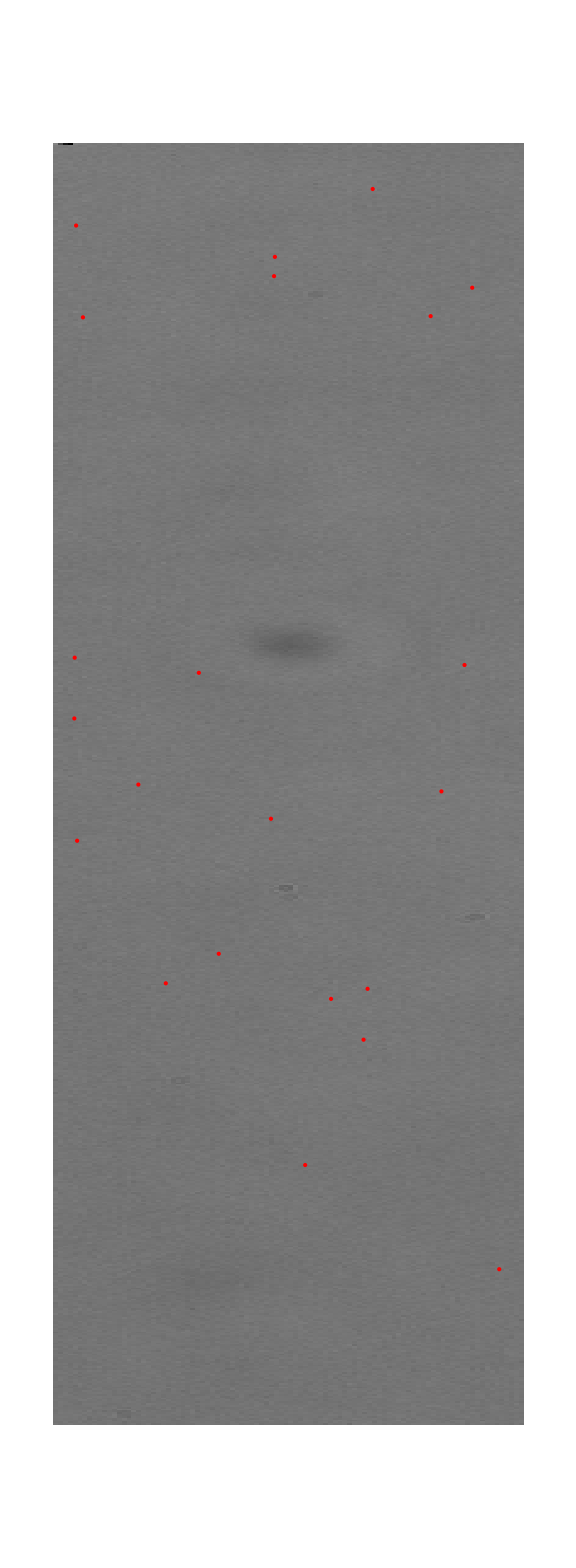
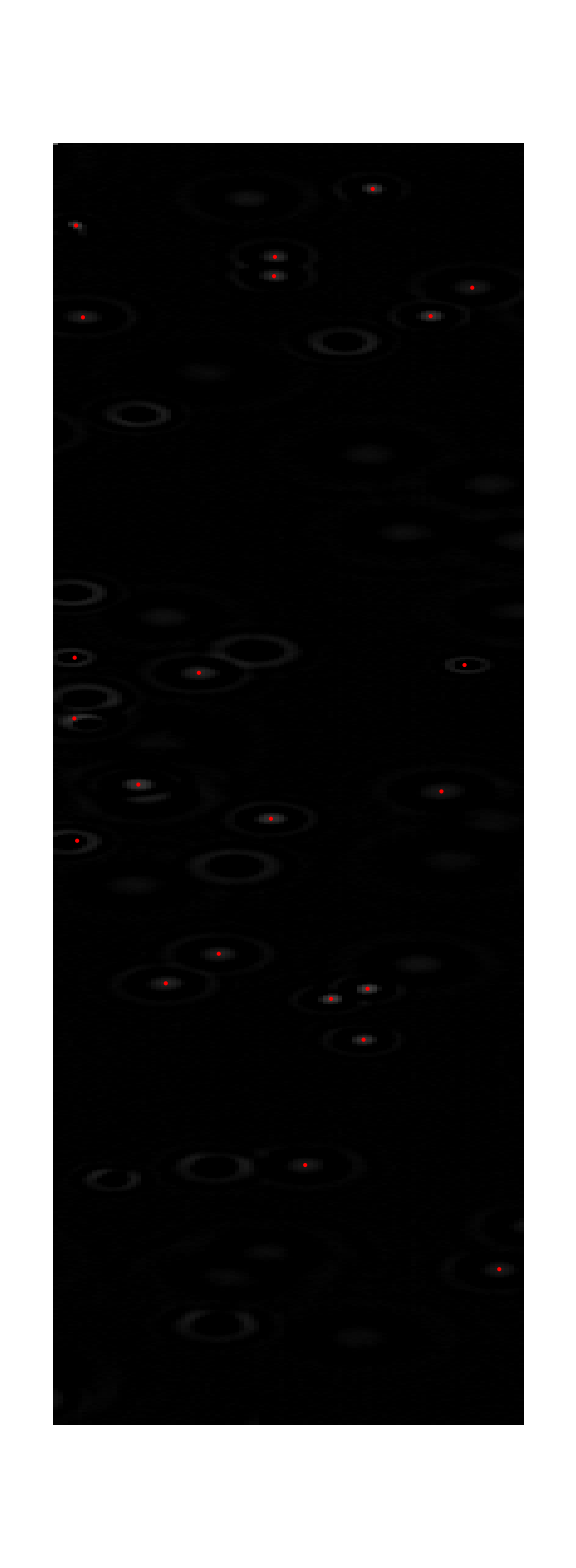
-Graphics--Graphics--Graphics--Graphics-

Area→{1→1.,2→19.5,3→1.,4→12.25,5→25.5,6→21.25,7→16.375,8→22.625,9→20.,10→20.125,11→14.75,12→37.375,13→43.,14→1.,15→2.25,16→2.,17→30.625,18→2.,19→19.25,20→2.25,21→1.,22→28.75,23→25.5,24→44.,25→30.,26→29.5,27→15.5,28→17.625,29→26.5,30→32.5,31→3.25,32→1.,33→1.,34→1.,35→24.5,36→25.875,37→19.5,38→20.5,39→20.5,40→8.625,41→13.125,42→14.5,43→10.625,44→6.,45→12.5,46→7.375,47→5.}

Elongation→{1→0.,2→0.344808,3→0.,4→0.431984,5→0.194149,6→0.120336,7→0.201281,8→0.100498,9→0.209431,10→0.709926,11→0.705128,12→0.328707,13→0.447433,14→0.,15→0.646447,16→0.5,17→0.361566,18→0.5,19→0.830974,20→0.646447,21→0.,22→0.0183082,23→0.155177,24→0.405177,25→0.447729,26→0.216733,27→0.166608,28→0.627274,29→0.160953,30→0.535107,31→0.728046,32→0.,33→0.,34→0.,35→0.0969503,36→0.116023,37→0.267993,38→0.0804413,39→0.0804413,40→0.717727,41→0.73852,42→0.0180195,43→0.682702,44→0.853615,45→0.,46→0.75664,47→0.823223}

FindThreshold→-0.0498085

```mathematica
frame =1 60 30         +17 30           -40+100;
frame = 10+300+100;
If[!IntegerQ[frame]|| 0>=frame||frame >  VideoLength[], frame = 1; Print@"Frame out of range. set to 1."];
ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list[[;;,{2,3}]]},ImageSize->Large]

curPos = VideoAnalyseFrame[frame]
Row[{
ShowTrackOverlayed[ VideoGet[frame] , curPos],
ShowTrackOverlayed[ BackgroundCurrent[], curPos],
ShowTrackOverlayed[ VideoGetForeground@VideoGet[frame] , curPos] ,
ShowTrackOverlayed[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] , curPos]
}]

"Area"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Area"]

"Elongation"-> ComponentMeasurements[ VideoFrameBinarize@VideoGetForeground@VideoGet[frame] ,"Elongation"]
"FindThreshold"-> FindThreshold@VideoGetForeground@VideoGet[frame]
```

## Step 5 - Select file range and run analysis

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[1]]
```

```mathematica
analyseTheseFiles=Select[
(StringReplace[VideoFile[], RegularExpression["\\d+.avi"]-> ""]~~ToString@#~~".avi")&/@ (Range[1,300])
,
FileExistsQ];
```

#### Background computation (optional)

```mathematica
BackgroungUpdate@bgAssociation[ VideoFile[]]
```

-Graphics-

```mathematica
DumpSave["background_images.mx", bgAssociation];
```

```mathematica
prepareBackgroundImages[analyseTheseFiles, 4]
```

Pre-computing background images for 26 files

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

VideoAddProcessRawFrame: new function count is 1

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

General::stop: Further output of FFImport :: notSupported will be suppressed during this calculation.

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

Cluter 1 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 2 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 3 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 4 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«1 more identical outputs»

Cluter 5 → -Graphics-

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

VideoAddProcessRawFrame: new function count is 1

«3 more identical outputs»

Cluter 6 → -Graphics-

Finised analysing all the backround images

#### Run the analysis

```mathematica
Monitor[
Do[ processVideo[analyseTheseFiles⟦i⟧], {i, Length[analyseTheseFiles] }],
Row[{"Analysing files: ",ProgressIndicator[i,{1,Length[analyseTheseFiles]}],i}," "]
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "video_tracking_paramters.txt"}]     ,
ToString@{
"ROI" -> ToString@ROICurrent[],
"VideoTracking" ->Options[VideoTracking]
}
]

Export[
 FileNameJoin[{ DirectoryName@First[analyseTheseFiles], "raw_points", "sample_frame.png"}]     ,
FFImport[VideoFile[], {"Frames", 1}]
];
```

===================== 200fps_s1.avi =====================

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

VideoAddProcessRawFrame: new function count is 1

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 9998]]

Analysis took (load + recognition): 25.4937 + 5828.25 = 5853.75 sec

Particles found: 189322, and problems were in 9890 frames

Background
-Graphics- | 344
-Graphics- | 959
-Graphics- | 2390
-Graphics- | 2634
-Graphics-
3418
-Graphics- | 4802
-Graphics- | 4870
-Graphics- | 7294
-Graphics- | 7679
-Graphics-
8879
-Graphics- | 8943
-Graphics- | 9207
-Graphics- | 9567
-Graphics- | 9812
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s1.csv

===================== 200fps_s2.avi =====================

FFImport::notSupported: Command not supported by FFImport[], faling back to Import[]

General::stop: Further output of FFImport :: notSupported will be suppressed during this calculation.

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 23.3803 + 6115.11 = 6138.49 sec

Particles found: 200614, and problems were in 9914 frames

Background
-Graphics- | 500
-Graphics- | 651
-Graphics- | 776
-Graphics- | 1008
-Graphics-
1092
-Graphics- | 3126
-Graphics- | 3205
-Graphics- | 3366
-Graphics- | 5487
-Graphics-
5980
-Graphics- | 7842
-Graphics- | 8604
-Graphics- | 8832
-Graphics- | 9099
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s2.csv

===================== 200fps_s3.avi =====================

VideoAddProcessRawFrame: new function count is 1

Buffer: [Warning] expected 10000 frames, but FFmpeg found 2661

Analysing: frames [[1 ;; 2661]]

Analysis took (load + recognition): 7.63211 + 1690.47 = 1698.1 sec

Particles found: 55365, and problems were in 2627 frames

Background
-Graphics- | 145
-Graphics- | 156
-Graphics- | 191
-Graphics- | 391
-Graphics-
403
-Graphics- | 668
-Graphics- | 1395
-Graphics- | 1407
-Graphics- | 1481
-Graphics-
1568
-Graphics- | 2274
-Graphics- | 2306
-Graphics- | 2447
-Graphics- | 2469
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s3.csv

===================== 200fps_s4.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 23.7719 + 6609.36 = 6633.13 sec

Particles found: 207231, and problems were in 9882 frames

Background
-Graphics- | 951
-Graphics- | 1718
-Graphics- | 1979
-Graphics- | 2280
-Graphics-
2956
-Graphics- | 5387
-Graphics- | 5579
-Graphics- | 6143
-Graphics- | 7017
-Graphics-
7130
-Graphics- | 7555
-Graphics- | 9159
-Graphics- | 9223
-Graphics- | 9450
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s4.csv

===================== 200fps_s5.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 23.8962 + 6991. = 7014.9 sec

Particles found: 194036, and problems were in 9946 frames

Background
-Graphics- | 880
-Graphics- | 1150
-Graphics- | 1607
-Graphics- | 2445
-Graphics-
2681
-Graphics- | 3292
-Graphics- | 3406
-Graphics- | 3776
-Graphics- | 3975
-Graphics-
9140
-Graphics- | 9350
-Graphics- | 9626
-Graphics- | 9682
-Graphics- | 9875
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s5.csv

===================== 200fps_s6.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 10000]]

Analysis took (load + recognition): 23.9515 + 6765.13 = 6789.08 sec

Particles found: 191959, and problems were in 9955 frames

Background
-Graphics- | 658
-Graphics- | 1671
-Graphics- | 2015
-Graphics- | 2841
-Graphics-
3653
-Graphics- | 4300
-Graphics- | 4352
-Graphics- | 4465
-Graphics- | 4975
-Graphics-
6375
-Graphics- | 7200
-Graphics- | 7393
-Graphics- | 8288
-Graphics- | 8953
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s6.csv

===================== 200fps_s7.avi =====================

VideoAddProcessRawFrame: new function count is 1

Analysing: frames [[1 ;; 4000]]

Analysing: frames [[4001 ;; 8000]]

Analysing: frames [[8001 ;; 8059]]

Analysis took (load + recognition): 21.0541 + 6114.26 = 6135.32 sec

Particles found: 185094, and problems were in 8024 frames

Background
-Graphics- | 234
-Graphics- | 553
-Graphics- | 823
-Graphics- | 1613
-Graphics-
3234
-Graphics- | 5183
-Graphics- | 5422
-Graphics- | 6440
-Graphics- | 6663
-Graphics-
6754
-Graphics- | 7178
-Graphics- | 7283
-Graphics- | 7352
-Graphics- | 7577
-Graphics-

Done: E:\2016-06-20\2\raw_points\200fps_s7.csv

E:\2016-06-20\2\raw_points\video_tracking_paramters.txt